# AMS-511 Foundations of Quantitative Finance

## Fall 2018 — Workshop — Due Monday 2018-12-10

## Examining the CAPM Against Actual Data

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

## Workshop Description

### Overview

The Capital Asset Pricing Model (CAPM) makes some specific predictions about the market for securities. There are two that we will address here. First, that the relationship between the return of an asset i and the market M follows the relationship

r_i(t)-r_f=β(r_M(t)-r_f)+ϵ_i(t)

And second, the proportion of asset i in the market (i.e., tangent) portfolio is

x_i∝β_i/Var[ϵ_i]

### Assignment

The assignment for this Workshop is to perform an analysis which computes the theoretical allocation, the actual allocation, and compares the two. You will be working with daily return data for the Dow Jones Industrial Index, which consists of 30 stocks, beginning 2013-01-02 and ending 2018-10-31, inclusive. The work involved is the following:

Load the necessary data. The required data files are all listed under Class 11 on the AMS 511 course page.

```mathematica
ClearAll["Global`*"]
xLocal[s_]:=FileNameJoin[{NotebookDirectory[],s}]
```

Import[ ] the daily return vector for the returns of the Dow Jones Industrial (DJI) Index which will represent the market. This is a vector of length 1471 with each element representing a different date.

```mathematica
vnDJIReturns=Import[xLocal["vnDJIReturns.m"]];
```

Import[ ] the daily returns matrix for the thirty members of the DJI. This is a matrix of dimension 1471×30 with each row representing a different date and each column a different stock.

```mathematica
mnReturns=Import[xLocal["mnReturns.m"]];
```

Import[ ] vectors representing the tickers of the DJI members (a vector of 30 strings).

```mathematica
vsDJI=Import[xLocal["vsDJI.m"]];
```

Import[ ] the calendar of dates (a vector of length 1471 with each element a date represented by a vector of length 3; alternately, it can be viewed as a 1471×3 matrix).

```mathematica
vxReturnCalendar=Import[xLocal["vxReturnCalendar.m"]];
```

All of the above are aligned properly.

Perform a CAPM  linear regression to estimate the betas and error variances of each member of the DJI. For simplicity assume an annual risk free rate of 2%. Approximate the daily rate as (1+0.02)^(1/250)-1.

```mathematica
nDailyRiskFree=(1+0.02)^(1/250)-1;
mnEstBetaErrVar =Table[Flatten[LinearModelFit[Transpose[{mnReturns⟦All, i⟧-nDailyRiskFree, vnDJIReturns-nDailyRiskFree}], x, x, IncludeConstantBasis->False][{"BestFitParameters", "EstimatedVariance"}]],{i,1,Length[vsDJI]}];
```

Use these estimates of the betas and error variances to compute the proportional allocations of each as predicted by the CAPM and normalize them so they sum to one.

```mathematica
vnCAPMAllocations=Table[mnEstBetaErrVar[[i,1]]/mnEstBetaErrVar[[i,2]],{i,1,Length[vsDJI]}];
vnCAPMNormalizedAllocations=vnCAPMAllocations/Total[vnCAPMAllocations]
```

{0.0647441,0.0327858,0.0160744,0.034469,0.0302568,0.0314087,0.0282011,0.0313904,0.0356802,0.0279125,0.0395825,0.0492432,0.037753,0.0226442,0.0318907,0.0484178,0.0536609,0.0287694,0.0236348,0.0261235,0.0196298,0.0321153,0.0291043,0.048101,0.02778,0.0545609,0.0224737,0.0382777,0.0147845,0.0185297}

Use FinancialData[ticker, “MarketCap”] to download the market capitalization of the members of the DJI and use them to compute the actual proportion of each in the DJI. Again, normalize their sum to one. I found that the DJI is calculated using the formula: DJI_Price = sum(price of each component)/dow_divisor. I get the price through FinancialData[] and the dow_divisor from http://www.wsj.com/mdc/public/page/2_3022-djiahourly.html. Then I calculate the weight of each component in the DJI. Also, DWDP and GS were not returning price data, so I removed the Missing values and all of the corresponding values from the CAPM allocations and the list of components in the DJI (variable vsDJI).

```mathematica
vnPricesDJI=FinancialData[vsDJI,"Price"]
nDJIPrice=FinancialData["DJI","Price"];
nDJIDivisor=0.14748071991788;

viMissingPositions=Position[vnPricesDJI,Missing][[All,1]];
vnPricesDJI=Delete[vnPricesDJI,List/@viMissingPositions];
vnCAPMNormalizedAllocations=Delete[vnCAPMNormalizedAllocations,List/@viMissingPositions];
vsDJI=Delete[vsDJI,List/@viMissingPositions];

vnDJIAllocations=(vnPricesDJI/nDJIDivisor)/nDJIPrice
```

{198.32,105.79,169.6,326.35,123.39,114.94,46.86,49.24,111.86,Missing[NotAvailable],76.54,Missing[NotAvailable],171.69,47.21,121.13,145.26,101.36,184.65,77.42,107.59,72.51,44.4,93.03,123,266.53,119.41,58.27,137.88,81.16,93.94}

{0.0550589,0.0293701,0.0470855,0.0906035,0.0342563,0.0319104,0.0130096,0.0136703,0.0310553,0.0212495,0.0476657,0.0131068,0.0336289,0.040328,0.0281402,0.0512638,0.0214939,0.0298698,0.0201307,0.0123266,0.0258276,0.0341481,0.0739958,0.0331514,0.0161773,0.0382792,0.0225322,0.0260802}

Plot the CAPM allocations estimated in (3.) against the market’s observed in (4.). Hover over the points to see the associated ticker. I included a 45 degree line on which the points would lie if the CAPM and DJI allocations were equal for each ticker.

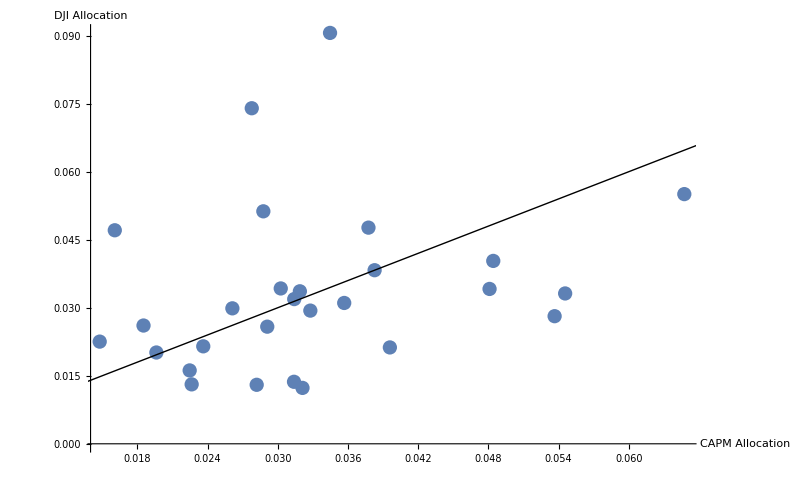

```mathematica
Show[ListPlot[MapThread[Tooltip,{Transpose[{vnCAPMNormalizedAllocations,vnDJIAllocations}],vsDJI}], AxesLabel->{"CAPM Allocation","DJI Allocation"}, ImageSize->800], Graphics[Line[{{0,0},{1,1}}]]]
```

Perform whatever additional comparisons you feel would be useful to characterize what you found. I created another plot that shows the same data in a different form. For each of the tickers, I removed the exchange so the tickers values fit nicely on the x-axis.

```mathematica
vsDJINoExchange=StringDelete[vsDJI,"NYSE:"];
vsDJINoExchange=StringDelete[vsDJINoExchange,"NASDAQ:"];
ListPlot[{MapThread[Tooltip,{vnCAPMNormalizedAllocations,vsDJINoExchange}],MapThread[Tooltip,{vnDJIAllocations,vsDJINoExchange}]},PlotLabels->{"CAPM Allocation","DJI Allocation"}, AxesLabel->{"Ticker","Allocation"},ImageSize->1000, Ticks->{Transpose[{Range[Length[vsDJINoExchange]],vsDJINoExchange}],Automatic}]
```

-Graphics-

What discrepancies do you note? How might you explain them?

```mathematica
Sort[Transpose[{vnPricesDJI,vsDJI}]]
Sort[Transpose[{vnCAPMNormalizedAllocations,vsDJI}]]
Sort[Transpose[{vnDJIAllocations,vsDJI}]]
vsDJIOrig=Import[xLocal["vsDJI.m"]];
Transpose[{mnEstBetaErrVar, vsDJIOrig}]
```

{{44.4,NYSE:PFE},{46.86,NASDAQ:CSCO},{47.21,NASDAQ:INTC},{49.24,NYSE:KO},{58.27,NYSE:VZ},{72.51,NYSE:NKE},{76.54,NYSE:XOM},{77.42,NYSE:MRK},{81.16,NASDAQ:WBA},{93.03,NYSE:PG},{93.94,NYSE:WMT},{101.36,NYSE:JPM},{105.79,NYSE:AXP},{107.59,NASDAQ:MSFT},{111.86,NYSE:DIS},{114.94,NYSE:CVX},{119.41,NYSE:UTX},{121.13,NYSE:IBM},{123,NYSE:TRV},{123.39,NYSE:CAT},{137.88,NYSE:V},{145.26,NYSE:JNJ},{169.6,NASDAQ:AAPL},{171.69,NYSE:HD},{184.65,NYSE:MCD},{198.32,NYSE:MMM},{266.53,NYSE:UNH},{326.35,NYSE:BA}}

{{0.0147845,NASDAQ:WBA},{0.0160744,NASDAQ:AAPL},{0.0185297,NYSE:WMT},{0.0196298,NYSE:NKE},{0.0224737,NYSE:VZ},{0.0226442,NASDAQ:INTC},{0.0236348,NYSE:MRK},{0.0261235,NASDAQ:MSFT},{0.02778,NYSE:UNH},{0.0282011,NASDAQ:CSCO},{0.0287694,NYSE:MCD},{0.0291043,NYSE:PG},{0.0302568,NYSE:CAT},{0.0313904,NYSE:KO},{0.0314087,NYSE:CVX},{0.0318907,NYSE:IBM},{0.0321153,NYSE:PFE},{0.0327858,NYSE:AXP},{0.034469,NYSE:BA},{0.0356802,NYSE:DIS},{0.037753,NYSE:HD},{0.0382777,NYSE:V},{0.0395825,NYSE:XOM},{0.048101,NYSE:TRV},{0.0484178,NYSE:JNJ},{0.0536609,NYSE:JPM},{0.0545609,NYSE:UTX},{0.0647441,NYSE:MMM}}

{{0.0123266,NYSE:PFE},{0.0130096,NASDAQ:CSCO},{0.0131068,NASDAQ:INTC},{0.0136703,NYSE:KO},{0.0161773,NYSE:VZ},{0.0201307,NYSE:NKE},{0.0212495,NYSE:XOM},{0.0214939,NYSE:MRK},{0.0225322,NASDAQ:WBA},{0.0258276,NYSE:PG},{0.0260802,NYSE:WMT},{0.0281402,NYSE:JPM},{0.0293701,NYSE:AXP},{0.0298698,NASDAQ:MSFT},{0.0310553,NYSE:DIS},{0.0319104,NYSE:CVX},{0.0331514,NYSE:UTX},{0.0336289,NYSE:IBM},{0.0341481,NYSE:TRV},{0.0342563,NYSE:CAT},{0.0382792,NYSE:V},{0.040328,NYSE:JNJ},{0.0470855,NASDAQ:AAPL},{0.0476657,NYSE:HD},{0.0512638,NYSE:MCD},{0.0550589,NYSE:MMM},{0.0739958,NYSE:UNH},{0.0906035,NYSE:BA}}

{{{0.560383,0.0000260431},NYSE:MMM},{{0.391303,0.0000359116},NYSE:AXP},{{0.246147,0.0000460754},NASDAQ:AAPL},{{0.370588,0.0000323497},NYSE:BA},{{0.340072,0.0000338187},NYSE:CAT},{{0.377731,0.000036186},NYSE:CVX},{{0.351367,0.000037489},NASDAQ:CSCO},{{0.455785,0.000043689},NYSE:KO},{{0.422472,0.0000356269},NYSE:DIS},{{0.329625,0.0000355328},NYSE:DWDP},{{0.453865,0.000034501},NYSE:XOM},{{0.422538,0.0000258184},NYSE:GS},{{0.439733,0.0000350466},NYSE:HD},{{0.300117,0.0000398788},NASDAQ:INTC},{{0.391563,0.0000369441},NYSE:IBM},{{0.548831,0.0000341069},NYSE:JNJ},{{0.455661,0.0000255501},NYSE:JPM},{{0.412032,0.0000430932},NYSE:MCD},{{0.33917,0.0000431791},NYSE:MRK},{{0.326168,0.0000375681},NASDAQ:MSFT},{{0.284641,0.0000436304},NYSE:NKE},{{0.419406,0.0000392945},NYSE:PFE},{{0.424545,0.0000438909},NYSE:PG},{{0.524427,0.000032805},NYSE:TRV},{{0.359309,0.0000389175},NYSE:UNH},{{0.521273,0.000028747},NYSE:UTX},{{0.345702,0.0000462845},NYSE:VZ},{{0.407334,0.0000320195},NYSE:V},{{0.23229,0.000047275},NASDAQ:WBA},{{0.297239,0.0000482666},NYSE:WMT}}

DWDP and GS prices are returning “Missing[Not Available]”, so I am unable to make any comments about them. I wrote the program to work around this problem. Also, if the prices are returned in the future, no adjustment to the program should be needed to run the program and see the plots for the allocations of all 30 stocks.

The CAPM allocations are for the portfolio that maximizes the ratio of reward (mean of daily returns) to risk (standard deviation of daily returns) . The DJI allocations are proportional to the price of the stock.

Based on how the CAPM allocations and DJI allocations are calculated, it wasn’t obvious to me at first if there would be any relation between their CAPM and DJI allocations. However, the plot in (5) shows a linear trend with a few outliers. So in general, DJI allocation increases as CAPM allocation increases. Now that I think more about it, I can see what causes that trend. A stock with increasing prices (and all other stock prices held equal) has an increasing proportion in the DJI by definition. Also, a stock with increasing prices will have an increasing reward, which helps increase the Sharpe ratio for that stock and in turn, its allocation in the CAPM portfolio.

BA, UNH and AAPL have much lower CAPM allocation than DJI allocation, shown clearly in (6). They have the 1st, 2nd and 6th highest DJI allocations, but have the 10th, 20th and 27th highest CAPM allocations. By definition, higher priced stocks have higher allocations in the DJI. The CAPM allocation increases as Beta increases, and increases as the volatility of the stock decreases. AAPL has a relatively low Beta and high volatility, so I see why it has a low CAPM allocation. The other 2 don’t have outstanding values for either Beta or volatility, so I see why they have their respective CAPM allocations. Since the DJI allocation is based solely on the current price, the allocations calculated here could rapidly change. However, the CAPM allocation is based on 1400+ daily returns, so it is more difficult for the Beta and volatility to significantly change and in turn cause a significant change in the allocation.